```mathematica
data=Import["C:\\Users\\usuario\\Google Drive\\iGEM\\DryLab\\Programas\\data.xlsx",{"Data",1}]
```

{{0.,0.},{0.25,1.11},{0.5,1.5},{0.75,1.885},{1.,2.32},{1.25,2.715},{1.5,3.12},{1.75,3.43},{2.,3.7},{2.25,3.93},{2.5,4.08667},{2.75,4.22},{3.,4.31333},{3.25,4.41667},{3.5,4.5},{3.75,4.5475},{4.,4.6},{4.25,4.6225},{4.5,4.64667},{4.75,4.6675},{5.,4.72},{5.25,4.7675},{5.5,4.8},{5.75,4.8},{6.,4.78},{6.25,4.76},{6.5,4.78},{6.75,4.78},{7.,4.78},{7.25,4.78},{7.5,4.02667},{7.75,3.88},{8.,3.85},{8.25,3.78},{8.5,3.78},{8.75,3.76},{9.,3.78},{9.25,3.78},{9.5,3.78},{9.75,3.78},{10.,3.76},{10.25,3.74},{10.5,3.72},{10.75,3.72},{11.,3.72},{11.25,3.72},{11.5,3.716},{11.75,3.69667},{12.,3.66},{12.25,3.64},{12.5,3.62},{12.75,3.62},{13.,3.62},{13.25,3.64},{13.5,3.66},{13.75,3.66},{14.,3.66},{14.25,3.66},{14.5,3.66},{14.75,3.66},{15.,3.66},{15.25,3.68},{15.5,3.72},{15.75,3.74},{16.,3.72},{16.25,3.69667},{16.5,3.66},{16.75,3.64},{17.,3.64},{17.25,3.64},{17.5,3.64},{17.75,3.66},{18.,3.66667}}

```mathematica
f=LinearModelFit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11},x]
```

FittedModel[0.190929+2.39872 x+«12»+4.7085×10^-8 x^10-3.7113×10^-10 x^11]

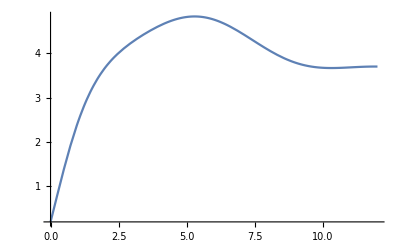

```mathematica
%Plot[f[x],{x,0,12},PlotRange->Full]
```

```mathematica
g1=Manipulate[
Plot[f[x],{x,0,n},PlotRange->{{0,12},{0,5}}],
{n,0.001,12}
]
```